```mathematica
Choose structures that do not shorten the intersection
```

```mathematica
pathToProject="/media/my_extra_space/projects/1510GPCR/";
pathToDump=pathToProject<>"dumps/";
Get[pathToDump<>"fromFurtherLabelingForChoosingIntersection.m"];
```

```mathematica
Omit structures from classes other than A, count number of resulting structures with/without chain repetitions
```

```mathematica
aClasses=Select[allStructures,(*Intersection[{#[[1]][[4]]},{"CRHR1","GCGR","GRM1","GRM5","SMO"}]=={}&];*)
Intersection[{#[[1]][[4]]},{23,24,25,26,27}]=={}&];
If[Intersection[{#[[1]][[4]]},{23,24,25,26,27}]!={},
AppendTo[thrown,{#[[1]][[1]]<>"_"<>#[[1]][[2]],"other Class"}];
,
];&/@allStructures;
Length@aClasses
Length@Union@(aClassesᵀ[[1]]ᵀ[[1]])
```

206

139

```mathematica
Mark residues that are not present in just few structures and take these structure names
```

```mathematica
allLabels={};
AppendTo[allLabels,#[[2]]ᵀ[[3]]]&/@aClasses;
allLabels=Flatten@allLabels;
tally=Drop[Tally[allLabels],1];
complements=Complement[allLabels,#[[2]]ᵀ[[3]]]&/@aClasses;
gatheredTally=Gather[tally,StringTake[#1[[1]],2]==StringTake[#2[[1]],2]&];

badIds={};
Do[subBadIds={};
If[((Length[aClasses]-gatheredTally[[i]]ᵀ[[2]][[#]]<6)&&(Length[aClasses]-gatheredTally[[i]]ᵀ[[2]][[#]])>0),t=" ";
Do[If[Intersection[complements[[j]],{gatheredTally[[i]]ᵀ[[1]][[#]]}]≠{},t=t<>aClasses[[j]][[1]][[1]]<>"_"<>aClasses[[j]][[1]][[2]]<>" ",];,{j,1,Length[aClasses]}];
AppendTo[subBadIds,{gatheredTally[[i]]ᵀ[[1]][[#]],t}];,]&/@Range[Length[gatheredTally[[i]]]];
AppendTo[badIds,subBadIds];,{i,1,numOfHelises}];
```

```mathematica
Show bar charts (structures lacking specific residues) and sieve based on that
```

```mathematica
barCharts={};
Do[AppendTo[barCharts,BarChart[Length[aClasses]-gatheredTally[[i]]ᵀ[[2]],ChartLabels->(StringDrop[#,2]&/@(gatheredTally[[i]]ᵀ[[1]])),ImageSize->1000,PlotLabel->Text[Style["number of structures lacking specific residue, helix "<>ToString[i],FontSize->20]],Epilog->(Text[Rotate[#[[2]],90 Degree],{Position[gatheredTally[[i]]ᵀ[[1]],#[[1]]][[1]][[1]],(Length[aClasses]-gatheredTally[[i]]ᵀ[[2]][[Position[gatheredTally[[i]]ᵀ[[1]],#[[1]]][[1]][[1]]]])+50}]&/@badIds[[i]])]];
,{i,1,numOfHelises}
];
```

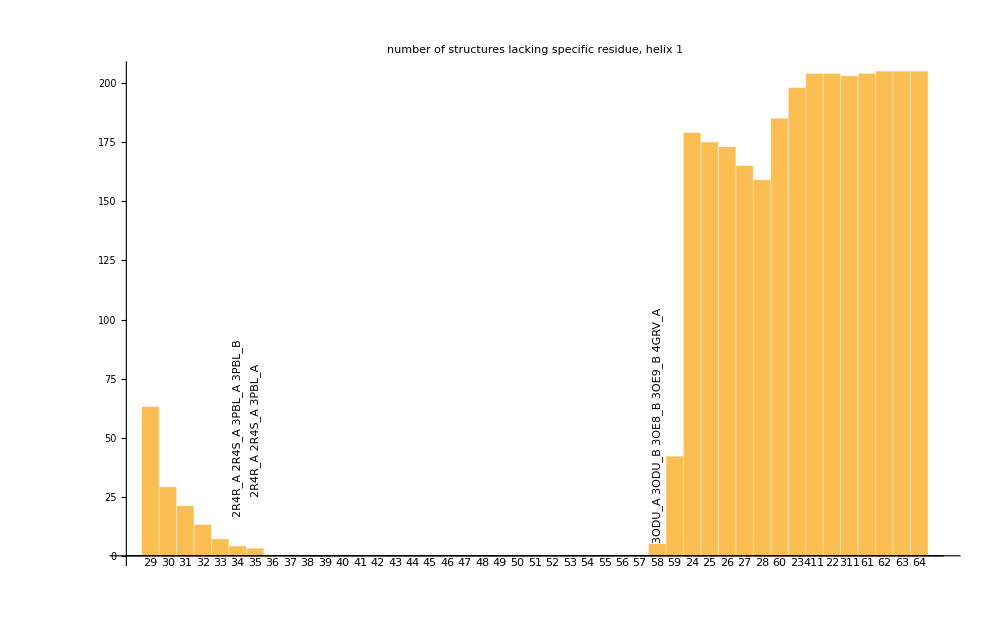

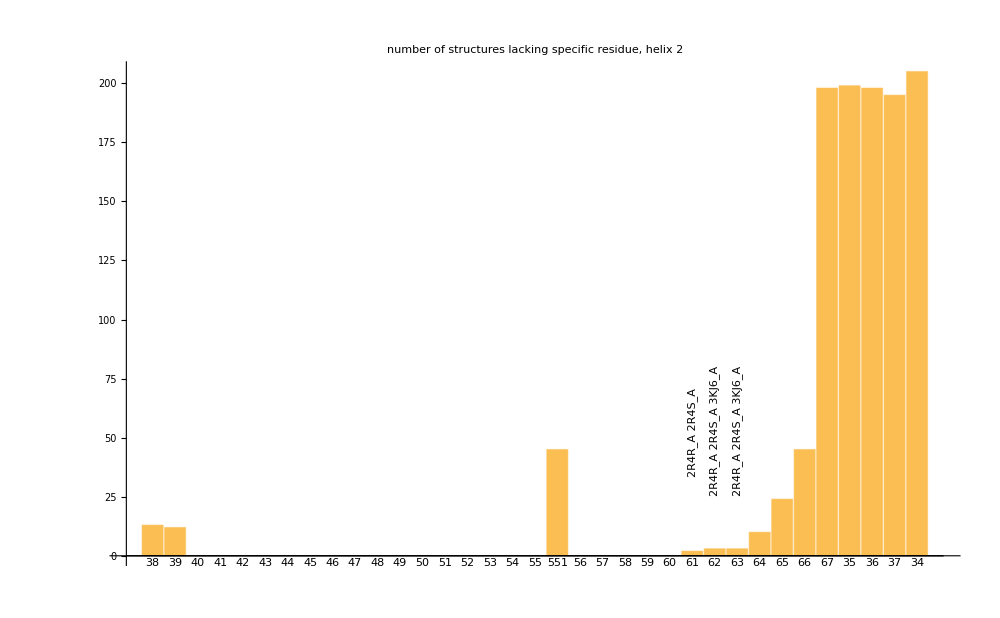

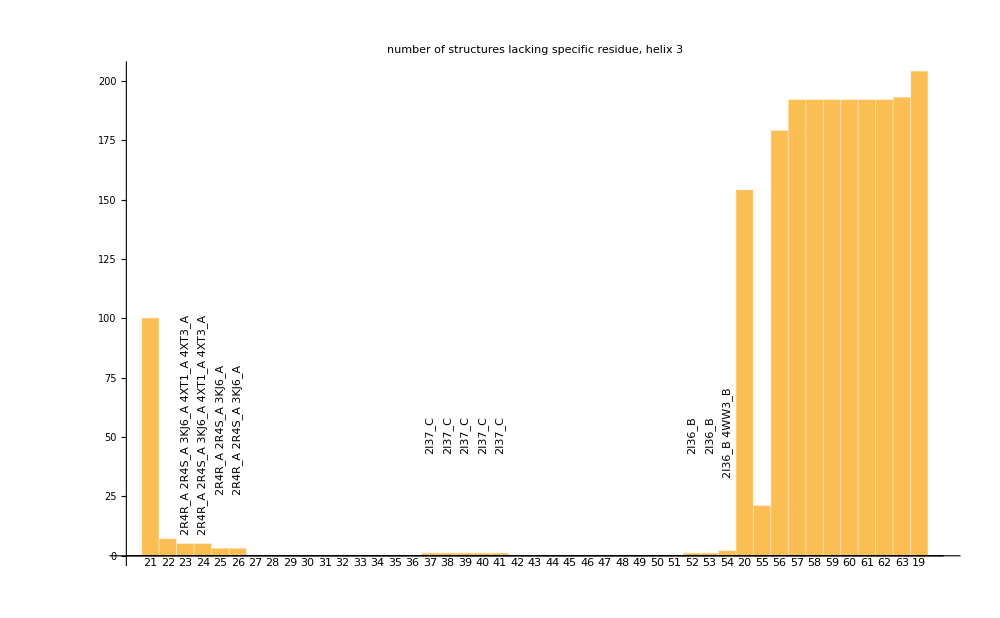

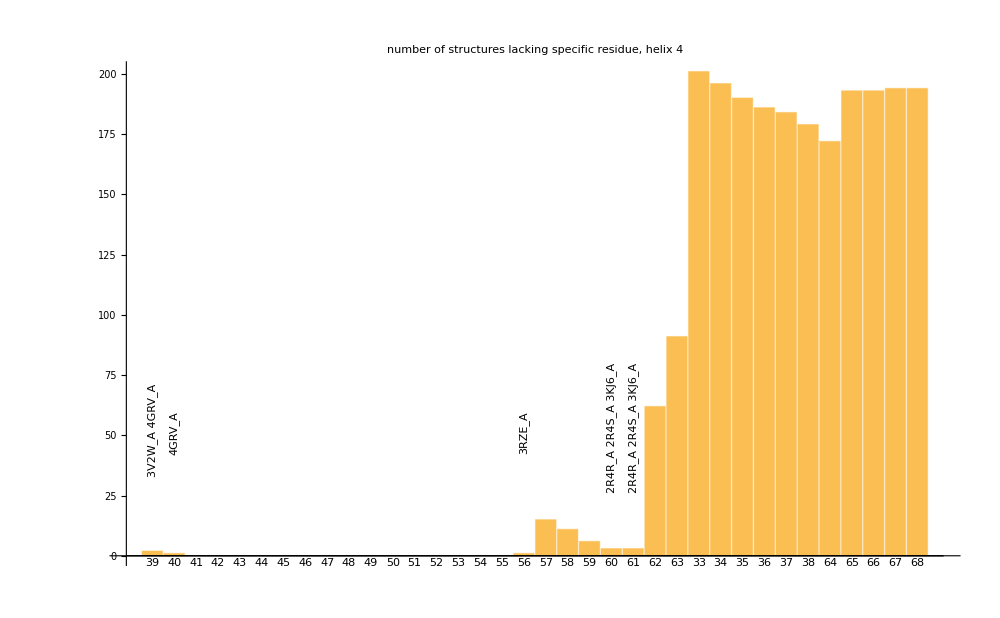

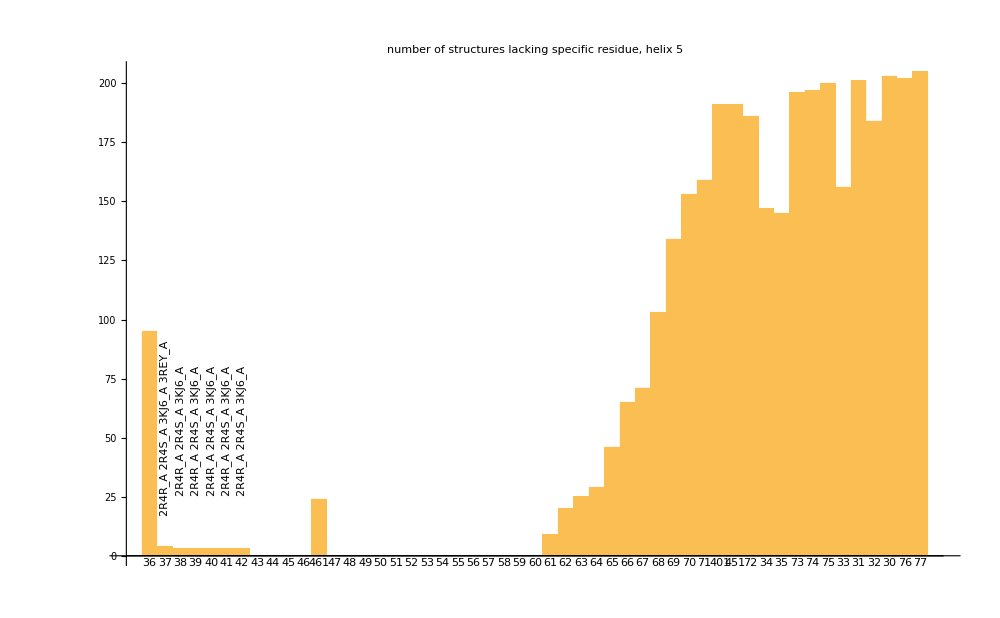

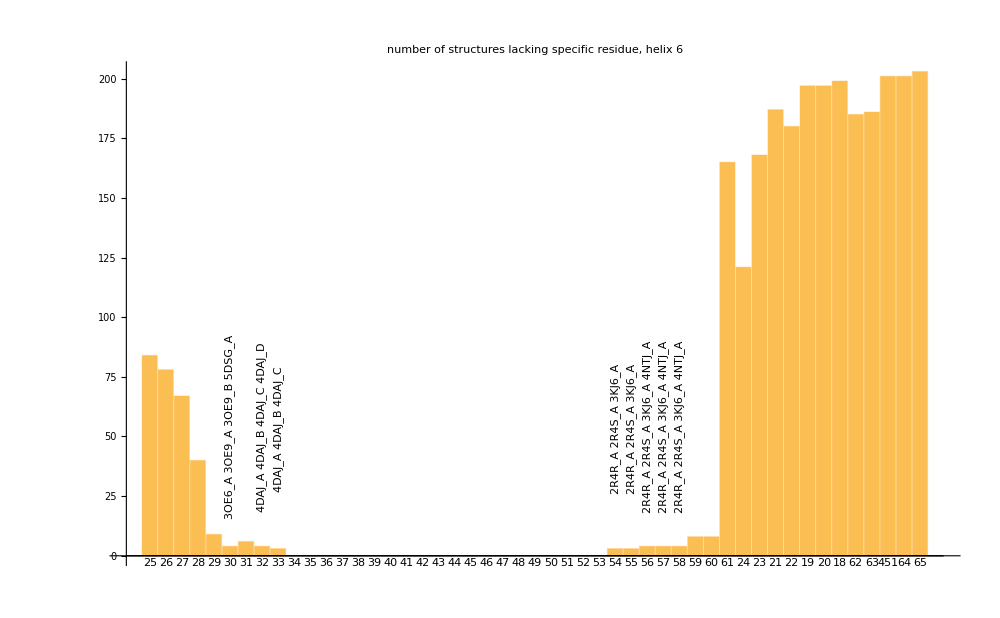

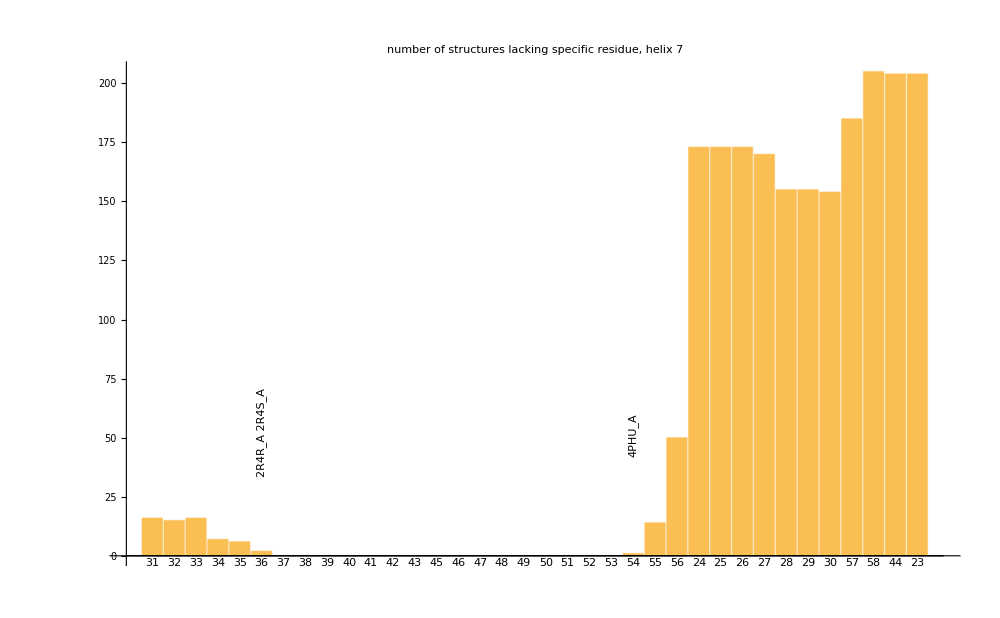

```mathematica
barCharts[[1]]
barCharts[[2]]
barCharts[[3]]
barCharts[[4]]
barCharts[[5]]
barCharts[[6]]
barCharts[[7]]
```

```mathematica
exclusions={"4DAJ_A","4DAJ_B","4DAJ_C","2I37_C","2I36_B","4WW3_B"};

aClasses=(If[Intersection[{#[[1]][[1]]<>"_"<>#[[1]][[2]]},exclusions]≠{},,#])&/@aClasses;

If[Intersection[{#[[1]][[1]]<>"_"<>#[[1]][[2]]},exclusions]≠{},AppendTo[thrown,{#[[1]][[1]]<>"_"<>#[[1]][[2]],"spoils intersection, but has other chains"}];,];&/@allStructures;

aClasses=Drop[(Union@aClasses),1];

allLabels={};
AppendTo[allLabels,#[[2]]ᵀ[[3]]]&/@aClasses;
allLabels=Flatten@allLabels;
tally=Drop[Tally[allLabels],1];
complements=Complement[allLabels,#[[2]]ᵀ[[3]]]&/@aClasses;
gatheredTally=Gather[tally,StringTake[#1[[1]],2]==StringTake[#2[[1]],2]&];

badIds={};
Do[subBadIds={};
If[((Length[aClasses]-gatheredTally[[i]]ᵀ[[2]][[#]]<6)&&(Length[aClasses]-gatheredTally[[i]]ᵀ[[2]][[#]])>0),t=" ";
Do[If[Intersection[complements[[j]],{gatheredTally[[i]]ᵀ[[1]][[#]]}]≠{},t=t<>aClasses[[j]][[1]][[1]]<>"_"<>aClasses[[j]][[1]][[2]]<>" ",];,{j,1,Length[aClasses]}];
AppendTo[subBadIds,{gatheredTally[[i]]ᵀ[[1]][[#]],t}];,]&/@Range[Length[gatheredTally[[i]]]];
AppendTo[badIds,subBadIds];,{i,1,numOfHelises}];

barCharts={};
Do[AppendTo[barCharts,BarChart[Length[aClasses]-gatheredTally[[i]]ᵀ[[2]],ChartLabels->(StringDrop[#,2]&/@(gatheredTally[[i]]ᵀ[[1]])),ImageSize->1000,PlotLabel->Text[Style["number of structures lacking specific residue, helix "<>ToString[i],FontSize->20]],Epilog->(Text[Rotate[#[[2]],90 Degree],{Position[gatheredTally[[i]]ᵀ[[1]],#[[1]]][[1]][[1]],(Length[aClasses]-gatheredTally[[i]]ᵀ[[2]][[Position[gatheredTally[[i]]ᵀ[[1]],#[[1]]][[1]][[1]]]])+50}]&/@badIds[[i]])]];
Export[pathToProject<>"figures/lackingResidues/"<>"lackingResiduesAll_"<>ToString[i]<>".png",barCharts[[i]]];,{i,1,numOfHelises}];
```

```mathematica
Gather labels present in every strucure, call it intersection. Show intersection length. Create lists of number of corresponding residues (for vmd script)
```

```mathematica
intersection=aClasses[[1]][[2]]ᵀ[[3]];
Do[
intersection=Intersection[intersection,aClasses[[n]][[2]]ᵀ[[3]]];
,{n,1,Length@aClasses}
];
intersection=Drop[intersection,1];
Length@intersection
resToSelect=ConstantArray[{},Length[aClasses]];
Do[curRes={};
Do[If[Intersection[{aClasses[[n]][[2]]ᵀ[[3]][[i]]},intersection]≠{},AppendTo[curRes,aClasses[[n]][[2]]ᵀ[[1]][[i]]],];,{i,1,Length[aClasses[[n]][[2]]]}];
resToSelect[[n]]=curRes;
Export[pathToProject<>"datFiles/resLists/"<>aClasses[[n]][[1]][[1]]<>"_"<>aClasses[[n]][[1]][[2]]<>"res.dat",resToSelect[[n]]];
,{n,1,Length[aClasses]}]
Export[pathToProject<>"datFiles/"<>"listOfAClassesIdsForPCA.dat",((#[[1]]<>"_"<>#[[2]])&/@(aClassesᵀ[[1]]))];
```

141

```mathematica
Save[pathToDump<>"fromChoosingIntersectionForPCAanalysis.m",{pathToProject,aClasses,intersection,families,thrown,numOfHelises}];
```